# Steiner's tree problem

## In large graphs

## Description

Steiner's tree problem
Input data:
G – undirected graph,
c : E(G) → R^+ – edge weight function,
T ⊆ V(G) – set of terminals
Output data:
steiner's tree for T in G.
i.e. output is G' – tree-subgraph of G : T ⊆ V(G') ∧ c(E(G')) → min.

## Packages

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
AppendTo[$Path, FileNameJoin[{Directory[], "packages"}]];
```

```mathematica
Needs["LeftistHeap`", "data_structures\\leftist_heap.wl"]
```

```mathematica
Needs["Steiner`Utilities`", "steiner_utilities.wl"]
```

```mathematica
Needs["Steiner`Algorithms`GraphUtilities`", "steiner_algorithms_graph_utilities.wl"]
```

```mathematica
Needs["Steiner`Generator`", "steiner_generator.wl"]
Needs["Steiner`SteinLib`", "steiner_steinlib.wl"]
```

```mathematica
Needs["Steiner`Visualization`", "steiner_visualization.wl"]
```

```mathematica
Needs["Steiner`Algorithms`Exact`", "steiner_algorithms_exact.wl"]
```

```mathematica
Needs["Steiner`Algorithms`Dijkstra`", "steiner_algorithms_dijkstra.wl"]
Needs["Steiner`Algorithms`Greedy`", "steiner_algorithms_greedy.wl"]
```

```mathematica
Needs["Steiner`Algorithms`Voronoi`", "steiner_algorithms_voronoi.wl"]
Needs["Steiner`Algorithms`Approximation`", "steiner_algorithms_approximation.wl"]
Needs["Steiner`Algorithms`LocalSearch`", "steiner_algorithms_local_search.wl"]
```

```mathematica
Needs["TestingSystem`", "testing_system.wl"]
```

## Input data

### Load pre-generated instances

#### Old

```mathematica
<<"dump/nice_15.mx"
```

```mathematica
<<"dump/nice_100.mx"
```

```mathematica
<<"dump/nice_grid.mx"
```

```mathematica
<<"dump/bip52p.mx"
```

#### New

```mathematica
(* Load generated in advance instances *)
```

```mathematica
<<"dump/nice_small.mx"
```

```mathematica
<<"dump/nice_medium.mx"
```

```mathematica
<<"dump/nice_grid_new.mx"
```

```mathematica
<<"dump/bip52p.mx"
```

### Generators

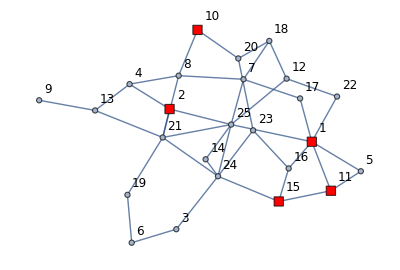

```mathematica
{graph15, weightAssociation15, terminals15} = generateSteinerProblemInstanceRG[25, 40, 5, WeightBounds ->{1, 1000}];
drawGraph[graph15, terminals15, VertexLabelStyle->Directive[Black,12],ImageSize->400]
```

```mathematica
DumpSave["dump/nice_small.mx", {graph15, weightAssociation15, terminals15}];
```

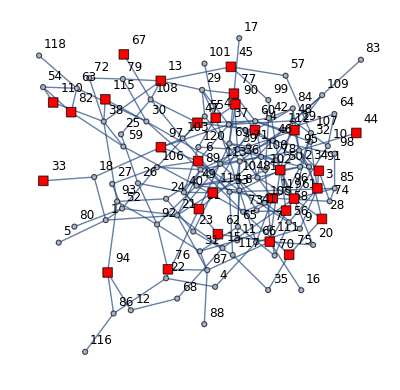

```mathematica
{graph100, weightAssociation100, terminals100} = generateSteinerProblemInstanceRG[150, 300, 40, WeightBounds ->{1, 1000}];
drawGraph[graph100, terminals100, VertexLabelStyle->Directive[Black,12], TerminalSize->1.25, ImageSize->400]
```

```mathematica
DumpSave["dump/nice_medium.mx", {graph100, weightAssociation100, terminals100}];
```

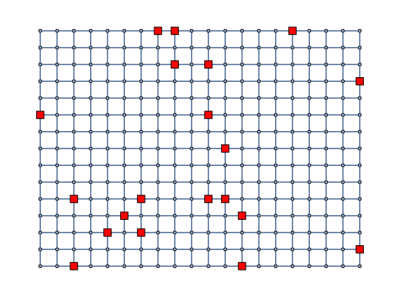

```mathematica
{graphGrid, terminalsGrid} = generateSteinerProblemInstanceGrid[15, 20, 20];
drawGraph[graphGrid, terminalsGrid, VertexLabelStyle->Directive[Black,12],ImageSize->400, VertexLabels->None]
```

```mathematica
DumpSave["dump/nice_grid_new_2.mx", {graphGrid, terminalsGrid}];
```

### SteinLib

```mathematica
getInstancesList["steinlib\\D"];
```

```mathematica
{stlibTestGraph, stlibTestWeights, stlibTestTerminals} = importSteinLibInstance["steinlib\\D\\d20.stp"];
```

```mathematica
VertexCount[stlibTestGraph]
EdgeCount[stlibTestGraph]
Length@stlibTestTerminals
```

1000

25000

500

```mathematica
getInstancesList["steinlib\\PUC"];
```

```mathematica
{stlibTestGraph, stlibTestWeights, stlibTestTerminals} = importSteinLibInstance["steinlib\\PUC\\bip52p.stp"];
```

```mathematica
VertexCount[stlibTestGraph]
EdgeCount[stlibTestGraph]
Length@stlibTestTerminals
```

2200

7997

200

```mathematica
DumpSave["dump/bip52p.mx", {stlibTestGraph, stlibTestTerminals}];
```

```mathematica
getInstancesList["steinlib\\SP"]
```

{steinlib\SP\antiwheel5.stp,steinlib\SP\design432.stp,steinlib\SP\oddcycle3.stp,steinlib\SP\oddwheel3.stp,steinlib\SP\se03.stp,steinlib\SP\w13c29.stp,steinlib\SP\w23c23.stp,steinlib\SP\w3c571.stp}

```mathematica
{stlibTestGraph, stlibTestWeights, stlibTestTerminals} = importSteinLibInstance["steinlib\\SP\\se03.stp"];
```

```mathematica
VertexCount[stlibTestGraph]
EdgeCount[stlibTestGraph]
Length@stlibTestTerminals
```

13

21

4

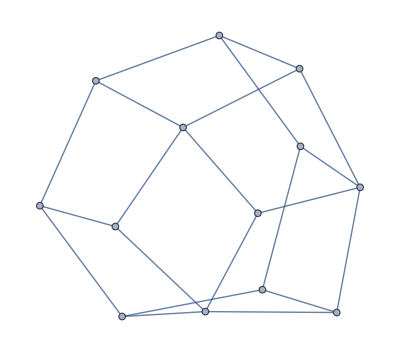
{-Graphics-,{1,8,10,12}}

```mathematica
DumpSave["dump/sp.mx", {stlibTestGraph, stlibTestTerminals}]
```

## Visualization

### Examples

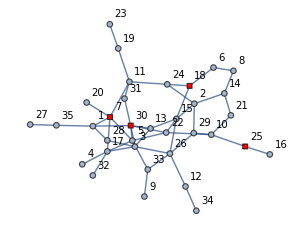

```mathematica
drawGraph[graph15,
terminals15,
VertexLabelStyle->Directive[Black,10],
VertexSize->0.85]
```

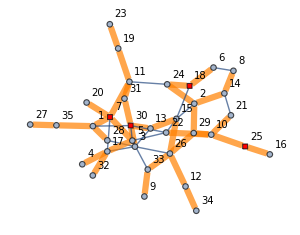

```mathematica
drawGraphSubgraph[graph15,
EdgeList@FindSpanningTree[graph15],
terminals15,
VertexLabelStyle->Directive[Black,10],
VertexSize->0.85]
```

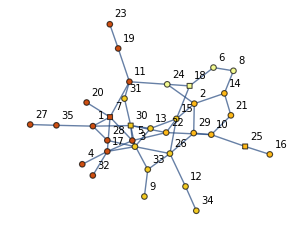

```mathematica
drawGraph[graph15,terminals15, VertexLabelStyle->Directive[Black,10],
VertexStyleFunc->voronoiVertexStyle[VertexList@graph15, Normal[dijkstraVoronoi[graph15, terminals15]["voronoi"]]],
VertexSize->0.85]
```

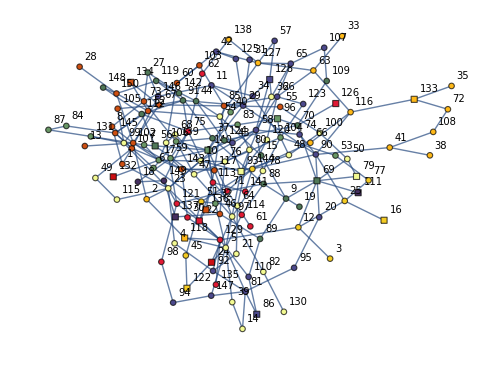

```mathematica
drawGraph[graph100, terminals100, VertexLabelStyle->Directive[Black,10],
VertexStyleFunc->voronoiVertexStyle[VertexList@graph100, Normal[dijkstraVoronoi[graph100, terminals100]["voronoi"]]],
TerminalSize->1.25, ImageSize->500]
```

### Animation export (test)

```mathematica
dijkstraVoronoi[graphGrid, terminalsGrid];
voronoiVertexStyle[VertexList@graphGrid, Normal[%["voronoi"]]]⟦%["order"]⟧;
a = Table[
drawGraph[
graphGrid,terminalsGrid, VertexLabelStyle->Directive[Black,10],
 VertexStyleFunc->%⟦;;step⟧,
ImageSize->500, VertexLabels->None,
VertexSize->Join[(# -> 0.6& /@ Complement[VertexList@graphGrid, terminalsGrid]), (# -> 0.8& /@terminalsGrid)],
Background->GrayLevel[0.975], BaseStyle->{Thick, EdgeForm[Thickness[0.005]]}]
,
{step, 1,VertexCount@graphGrid, 1}];
```

```mathematica
Export["visual/steiner_voronoi_grid.gif", a, "GIF" , "ControlAppearance"->None,"DisplayDurations"->0.025,ImageSize->700];
```

## Exact algorithms

### Dynamic programming (Dreyfus – Wagner) [1][3][4][5]

#### Description

```mathematica
-Graphics-
-Graphics-
```

Asymptotic time is : O (3^t n+2^t n^2+poly()), where t = #Terminals. n = #Vertices.

Better not to use on instances with t >= 7, or n, m > 50.

#### Examples

{0.206017,Null}

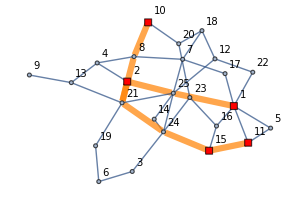
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1605.

```mathematica
({resultDreyfusWagner15, treeDreyfusWagner15} = runDreyfusWagner[graph15, terminals15]);//AbsoluteTiming
gridResult[graph15,  terminals15, treeDreyfusWagner15, resultDreyfusWagner15]
```

{266.469,Null}

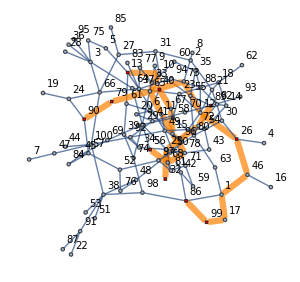
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 7175.

```mathematica
({resultDreyfusWagner100, treeDreyfusWagner100} = runDreyfusWagner[graph100, terminals100]);//AbsoluteTiming
gridResult[graph100,  terminals100, treeDreyfusWagner100, resultDreyfusWagner100]
```

{0.0356059,Null}

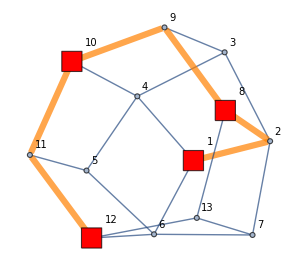
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 12.

```mathematica
({resultDreyfusWagnerStlibTest, treeDreyfusWagnerStlibTest} = runDreyfusWagner[stlibTestGraph, stlibTestTerminals]);//AbsoluteTiming
gridResult[stlibTestGraph, stlibTestTerminals, treeDreyfusWagnerStlibTest, resultDreyfusWagnerStlibTest]
```

{115.794,Null}

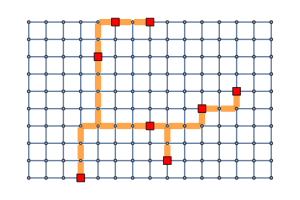
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 25.

```mathematica
({resultDreyfusWagnerGrid, treeDreyfusWagnerGrid} = runDreyfusWagner[graphGrid, terminalsGrid]);//AbsoluteTiming
gridResult[graphGrid, terminalsGrid, treeDreyfusWagnerGrid, resultDreyfusWagnerGrid, VertexLabels->None]
```

## Voronoi

### Examples

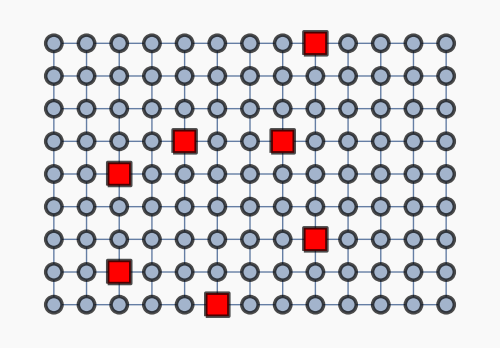

```mathematica
drawGraph[graphGrid, terminalsGrid,
 VertexLabelStyle->Directive[Black,10], ImageSize->500, VertexLabels->None,
VertexSize->Join[(# -> 0.5&/@ Complement[VertexList@graphGrid, terminalsGrid]), (# -> 0.8& /@terminalsGrid)],
Background->GrayLevel[0.975], BaseStyle->{Thick, EdgeForm[Thickness[0.005]]}]
```

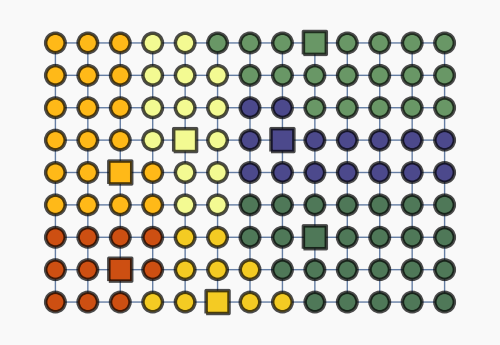

```mathematica
drawGraph[graphGrid, terminalsGrid, VertexLabelStyle->Directive[Black,10],
VertexStyleFunc->voronoiVertexStyle[VertexList@graphGrid, Normal[dijkstraVoronoi[graphGrid, terminalsGrid]["voronoi"]]],
ImageSize->500, VertexLabels->None,
VertexSize->Join[(# -> 0.6& /@ Complement[VertexList@graphGrid, terminalsGrid]), (# -> 0.8& /@terminalsGrid)],
Background->GrayLevel[0.975], BaseStyle->{Thick, EdgeForm[Thickness[0.005]]}]
```

## Leftist Heap

### Examples

```mathematica
ClearAll[a,b,c]
```

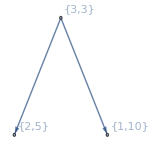
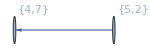

```mathematica
a = leftistHeapHeapify[{{1, 10}, {2, 5}, {3, 3}}];
b = leftistHeapHeapify[{{4, 7}, {5, 2}}];
Row[{leftistHeapDraw[a], leftistHeapDraw[b]}]
```

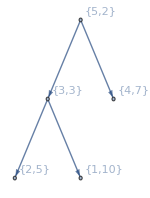

```mathematica
leftistHeapMeldClearly[c,a, b];
leftistHeapDraw[c]
```

5

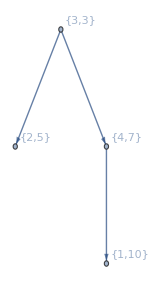

```mathematica
leftistExtractMin@c
leftistHeapDraw[c]
```

```mathematica
ClearAll[a,b,c]
```

## Approximation algorithms

### 2-approximation (Kou – Markowsky – Berman) [1][2]

#### Description

```mathematica
-Graphics-
-Graphics-
-Graphics-
```

### 2-approximation (Mehlhorn) [7][8]

#### Description

Mehlhorn's algorithm (improvement of previous algorithm):
1. Build Auxilary graph (AG):
	- build Voronoi diagram of graph.
	- create new graph AG.
	- for all border edges (u, v) add to AG edge (voronoi_center[u], voronoi_center[v]) with weight distance(voronoi_center[u], u) + distance(voronoi_center[v], v) + weight[(u, v)].
2. Find MinSpanningTree in AG.
3. Find original graph subgraph of short-paths accordind to auxilary spanning tree.
4. Find MinSpanningTree of that subgraph.
5. Cut it, to make Steiner-tree.

### Examples

#### 15

```mathematica
(treeKouMarkowskyBerman15 = runKouMarkowskyBerman[graph15, terminals15]);//AbsoluteTiming
resultKouMarkowskyBerman15 = edgeWeightSum[graph15, treeKouMarkowskyBerman15]
gridResult[graph15,  terminals15, treeKouMarkowskyBerman15, resultKouMarkowskyBerman15]
```

{0.054568,Null}

1605

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1605

```mathematica
(treeMehlhorn15 = runMehlhorn[graph15, terminals15]);//AbsoluteTiming
resultMehlhorn15 = edgeWeightSum[graph15, treeMehlhorn15]
gridResult[graph15,  terminals15, treeMehlhorn15, resultMehlhorn15]
```

{0.90331,Null}

1605

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1605

#### 100

{0.127007,Null}

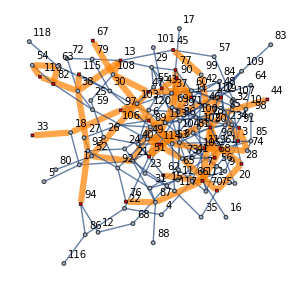
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 13947

```mathematica
(treeKouMarkowskyBerman100 = runKouMarkowskyBerman[graph100, terminals100]);//AbsoluteTiming
resultKouMarkowskyBerman100 = edgeWeightSum[graph100, treeKouMarkowskyBerman100];
gridResult[graph100,  terminals100, treeKouMarkowskyBerman100, resultKouMarkowskyBerman100]
```

```mathematica
(treeMehlhorn100 = runMehlhorn[graph100, terminals100]);//AbsoluteTiming
resultMehlhorn100 = edgeWeightSum[graph100, treeMehlhorn100];
gridResult[graph100,  terminals100, treeMehlhorn100, resultMehlhorn100]
```

{0.0184657,Null}

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 13947

#### Stlib

```mathematica
TimeConstrained[(treeKouMarkowskyBermanStlib = runKouMarkowskyBerman[stlibTestGraph, stlibTestTerminals]);//AbsoluteTiming,
300, "More than 300 sec."]
```

More than 300 sec.

```mathematica
(treeMehlhornStlibTest = runMehlhorn[stlibTestGraph, stlibTestTerminals]);//AbsoluteTiming
resultMehlhornStlibTest = edgeWeightSum[stlibTestGraph, treeMehlhornStlibTest]
steinerSolutionQ[treeMehlhornStlibTest, stlibTestTerminals]
gridResult[stlibTestGraph, stlibTestTerminals, treeMehlhornStlibTest, resultMehlhornStlibTest];
```

{0.537329,Null}

37452

True

#### GridGraph

{0.0295588,Null}

66

True

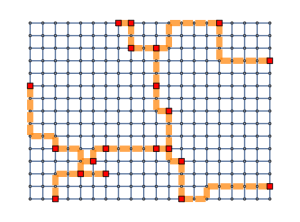
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 66

```mathematica
(treeMehlhornGridTest = runMehlhorn[graphGrid, terminalsGrid]);//AbsoluteTiming
resultMehlhornGridTest = edgeWeightSum[graphGrid, treeMehlhornGridTest]
steinerSolutionQ[treeMehlhornGridTest, terminalsGrid]
gridResult[graphGrid, terminalsGrid, treeMehlhornGridTest, resultMehlhornGridTest, VertexLabels->None]
```

## Greedy algorithms [6][7]

### Shortest-path heuristic (SPH)

#### Description

Algorithms starts from one-vertex tree containing only terminal t and consequently adds paths to closest (to tree vertices) terminal, that was not added yet.

### Repeated SPH (RSPH)

#### Description

In RSPH basic SPH is being used multiple times from different start terminals, and then best solution is chosen.
RSPH uses universal distance-matrix for all starts of SPH to avoid recomputations.

### Examples

```mathematica
(treeRSP15 = steinerRepeatedShortestPathHeuristic[graph15, terminals15, 100])//AbsoluteTiming
resultRSP15 = edgeWeightSum[graph15, treeRSP15]
steinerSolutionQ[treeRSP15, terminals15]
gridResult[graph15,  terminals15, treeRSP15, resultRSP15]
```

{0.0283555,{11<->15,15<->24,24<->21,21<->2,21<->8,2<->25,25<->1,8<->10}}

1605

True

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1605

{0.779364,Null}

True

13515

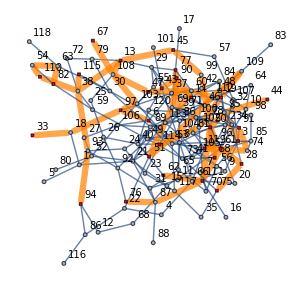
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 13515

```mathematica
(treeSP100 = steinerRepeatedShortestPathHeuristic[graph100, terminals100, 100]);//AbsoluteTiming
steinerSolutionQ[treeSP100, terminals100]
resultSP100 = edgeWeightSum[graph100, treeSP100]
gridResult[graph100,  terminals100, treeSP100, resultSP100]
```

{0.006499,Null}

True

12

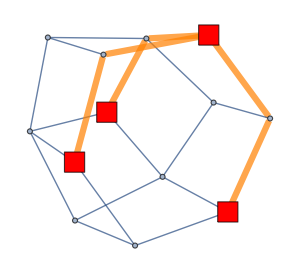
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 12

```mathematica
(treeSPStlib = steinerRepeatedShortestPathHeuristic[stlibTestGraph, stlibTestTerminals, 100]);//AbsoluteTiming
steinerSolutionQ[treeSPStlib, stlibTestTerminals]
resultSPStlib= edgeWeightSum[stlibTestGraph, treeSPStlib]
gridResult[stlibTestGraph,  stlibTestTerminals, treeSPStlib, resultSPStlib, VertexLabels->None]
```

{0.772038,Null}

True

47

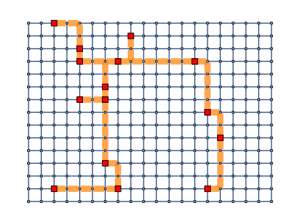
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 47

```mathematica
(treeSPGrid = steinerRepeatedShortestPathHeuristic[graphGrid, terminalsGrid, 5]);//AbsoluteTiming
steinerSolutionQ[treeSPGrid, terminalsGrid]
resultSPGrid = edgeWeightSum[graphGrid, treeSPGrid]
gridResult[graphGrid,  terminalsGrid, treeSPGrid, resultSPGrid, VertexLabels->None]
```

```mathematica
(* Big stlib instance *)
(treeSPStlib = steinerRepeatedShortestPathHeuristic[stlibTestGraph, stlibTestTerminals, 100]);//AbsoluteTiming
steinerSolutionQ[treeSPStlib, stlibTestTerminals]
resultSPStlib= edgeWeightSum[stlibTestGraph, treeSPStlib]
```

{101.29,Null}

True

28895

#### anim

```mathematica
gridSPHFramesReap = Reap[steinerShortestPathHeuristic[graphGrid, terminalsGrid, RandomChoice[terminalsGrid]], "SolutionChange"]⟦2, 1⟧ ;
gridSPHFrames= Grid[{{drawGraphSubgraph[graphGrid, #⟦1⟧, terminalsGrid, VertexLabels->None]}, {#⟦2⟧}}]&/@gridSPHFramesReap;
```

```mathematica
DumpSave["dump\\presentation_greedy", gridSPHFrames];
```

## Local-search algorithms [7]

### General Description

fact: Given weighted graph G, for any S - feasible solution of steiner tree problem, it is true that MST[V(S)] ≤ S (by total weight), where MST[S] -- minimal spanning tree of vertices X in G. 

def: Steiner-vertex is a vertex is S that is not terminal, i.e. S \ T.
def. Crucial-vertex is a vertex in S that is either terminal or has degree >= 3 in S.

There are 3 local-search algorithms below:
1) Steiner-vertex insertion. (VI)
2) Steiner-vertex elimination. (VE)
3) Key-path exchange. (PE)

First 2 algorithms are based on principle of editing V(T) (inserting or eliminating steiner-vertex), and recalculating MST, trying to get improvement of solution.

Key-path exchange algorithm for any path between 2 crusial vertices, that contain's no more crucial vertices, tries to elimnate it and then reconnect resulting graph components in shortest possible way (so, exchange paths).

Also there are 2 combinations of algorithms above presented:
1) VIVE
2) PEVIVE

### Steiner-Vertex Insertion

#### Examples

```mathematica
tree = steinerVertexInsertionFixedPoint[graph15, treeMehlhorn15]
steinerSolutionQ[tree, terminals15]
edgeWeightSum[graph15, tree]
edgeWeightSum[graph15, treeMehlhorn15]
```

{2<->25,2<->21,25<->1,11<->15,15<->24,21<->24,21<->8,8<->10}

True

1605

1605

```mathematica
tree = steinerVertexInsertionFixedPoint[graph100, treeMehlhorn100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeMehlhorn100]
```

{33<->18,18<->97,97<->103,97<->6,19<->71,19<->102,71<->89,89<->21,21<->52,47<->106,47<->108,47<->60,106<->52,114<->102,13<->108,13<->38,108<->103,108<->67,60<->39,39<->77,50<->95,50<->96,50<->111,50<->99,50<->58,95<->3,95<->44,96<->119,119<->74,119<->53,111<->61,111<->62,111<->87,45<->99,61<->28,28<->75,74<->91,53<->103,51<->69,51<->104,69<->90,90<->43,90<->14,104<->49,49<->73,75<->73,87<->76,110<->38,110<->54,38<->93,38<->115,94<->93,54<->63,82<->63}

True

13947

13947

```mathematica
tree = steinerVertexInsertionFixedPoint[graphGrid, treeMehlhornGridTest];
steinerSolutionQ[tree, terminalsGrid]
edgeWeightSum[graphGrid, tree]
edgeWeightSum[graphGrid, treeMehlhornGridTest]
```

True

119

119

```mathematica
tree = steinerVertexInsertionFixedPoint[stlibTestGraph, treeMehlhornStlibTest];
steinerSolutionQ[tree, stlibTestTerminals]
edgeWeightSum[stlibTestGraph, tree]
edgeWeightSum[stlibTestGraph, treeMehlhornStlibTest]
```

True

540

542

### Steiner-Vertex Elimination

#### Examples

```mathematica
tree = steinerVertexEliminationFixedPoint[graph15, treeMehlhorn15, terminals15]
steinerSolutionQ[tree, terminals15]
edgeWeightSum[graph15, tree]
edgeWeightSum[graph15, treeMehlhorn15]
```

{2<->25,2<->21,25<->1,11<->15,15<->24,21<->24,21<->8,8<->10}

True

1605

1605

```mathematica
tree = steinerVertexEliminationFixedPoint[graph100, treeMehlhorn100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeMehlhorn100]
```

{3<->95,6<->97,13<->38,13<->45,13<->108,14<->90,18<->33,18<->97,19<->71,21<->52,21<->89,21<->114,28<->61,28<->75,38<->93,38<->110,38<->115,39<->60,39<->77,43<->90,44<->95,45<->99,47<->60,47<->106,47<->108,49<->73,49<->104,50<->58,50<->95,50<->96,50<->99,50<->111,51<->69,51<->104,52<->106,54<->63,54<->110,61<->111,62<->111,63<->82,67<->108,69<->90,71<->89,73<->75,74<->91,74<->119,76<->87,87<->111,93<->94,96<->119,97<->103,103<->108}

True

13784

13947

```mathematica
tree = steinerVertexEliminationFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid];
steinerSolutionQ[tree, terminalsGrid]
edgeWeightSum[graphGrid, tree]
edgeWeightSum[graphGrid, treeMehlhornGridTest]
```

True

119

119

```mathematica
tree = steinerVertexEliminationFixedPoint[stlibTestGraph, treeMehlhornStlibTest, stlibTestTerminals];
steinerSolutionQ[tree, stlibTestTerminals]
edgeWeightSum[stlibTestGraph, tree]
edgeWeightSum[stlibTestGraph, treeMehlhornStlibTest]
```

True

27090

37452

### VIVE

#### Examples

```mathematica
tree = steinerVIVEFixedPoint[graph15, treeMehlhorn15, terminals15]
steinerSolutionQ[tree, terminals15]
edgeWeightSum[graph15, tree]
edgeWeightSum[graph15, treeMehlhorn15]
```

{2<->25,2<->21,25<->1,11<->15,15<->24,21<->24,21<->8,8<->10}

True

1605

1605

```mathematica
tree = steinerVIVEFixedPoint[graph100, treeMehlhorn100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeMehlhorn100]
```

{3<->95,6<->97,13<->38,13<->45,13<->108,14<->90,18<->33,18<->97,19<->71,21<->52,21<->89,21<->114,28<->61,28<->75,38<->93,38<->110,38<->115,39<->60,39<->77,43<->90,44<->95,45<->99,47<->60,47<->106,47<->108,49<->73,49<->104,50<->58,50<->95,50<->96,50<->99,50<->111,51<->69,51<->104,52<->106,54<->63,54<->110,61<->111,62<->111,63<->82,67<->108,69<->90,71<->89,73<->75,74<->91,74<->119,76<->87,87<->111,93<->94,96<->119,97<->103,103<->108}

True

13784

13947

```mathematica
tree = steinerVIVEFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid];
steinerSolutionQ[tree, terminalsGrid]
edgeWeightSum[graphGrid, tree]
edgeWeightSum[graphGrid, treeMehlhornGridTest]
```

True

119

119

```mathematica
tree =  steinerVIVEFixedPoint[graph100, treeSP100, terminals100]
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeSP100]
```

{1<->8,1<->23,5<->81,5<->93,5<->118,8<->102,10<->23,10<->93,16<->25,17<->102,17<->132,22<->113,24<->97,25<->90,26<->58,26<->85,26<->120,45<->51,45<->122,47<->56,47<->76,47<->97,47<->139,51<->144,58<->74,58<->128,67<->102,67<->134,69<->70,69<->79,69<->111,70<->96,70<->126,74<->90,75<->83,75<->113,75<->149,76<->80,80<->93,81<->86,83<->96,85<->117,90<->116,90<->144,93<->120,113<->140,116<->133,117<->136,137<->149,139<->140}

True

16725

18762

```mathematica
tree = steinerVIVEFixedPoint[stlibTestGraph, treeMehlhornStlibTest, stlibTestTerminals];
steinerSolutionQ[tree, stlibTestTerminals]
edgeWeightSum[stlibTestGraph, tree]
edgeWeightSum[stlibTestGraph, treeMehlhornStlibTest]
```

True

27090

37452

True

62

64

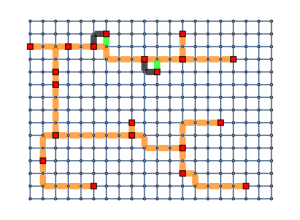
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 64→62

```mathematica
tree = steinerVIVEFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid];
steinerSolutionQ[tree, terminalsGrid]
edgeWeightSum[graphGrid, tree]
edgeWeightSum[graphGrid, treeMehlhornGridTest]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeMehlhornGridTest, edgeWeightSum[graphGrid, treeMehlhornGridTest]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

### Key-Path Exchange

#### Description [7]

Algorithm implementation is almost straight to one descripted in [7].

For reduction of shortest-path recalculations voronoi diagramms are used (dijkstraVoronoi), with centers in each vertex of original solution. Repairing of diagramm (in case of path elimination) are based on rerunning main step of dijkstraVoronoi, starting in border points of empty zones.

nb: Voronoi diagramm - partition of vertices of graph into sets, with respect to given set of centers C, such that vertex u is in one set with center c iff c is closest of centers to u (breaking of ties is irrelevant). Construction of diagramm implemented by running Dijkstra's algorithm simultaniously from all centers, additionally keeping an array of current centers for each vertex [7].

Key-path exchange algorithm main steps [7]: 
1. Build voronoi diagramm with centers in all nodes of base solution.
2. For each center priority queue (leftist heap) (meldable heap) is created. Then all edges, that are boundary (i.e. end points of edge have different centers in voronoi diagramm) are pushed to each of its centers heap with path cost as weight. 
3. Graph is being rooted, and is traversed from leaves to tops (dfs).
4. On accending of dfs key-paths are being found.
5. After sub-tree is traversed, all heaps in it's vertices are being meld in one.
6. Vertices are also carried in Disjoint Sets for easyness of checking which subtree they belong to.
7. After key-path is found, it is being tested on possibility of exchange. Algorithms finds best border-edge while repairing voronoi and testing saved boundary edges.

Also, implementation of algorithms allows multiple moves (exchanges) in one full iteration (by blocking possibilites for certain vertices to be in exchanging path, to avoid disconnection of graph).

```mathematica
-Graphics-
-Graphics-
```

#### Examples

```mathematica
tree =  steinerKeyPathExchangeFixedPoint[graph15, treeMehlhorn15, terminals15]
edgeWeightSum[graph15, tree]
edgeWeightSum[graph15, treeMehlhorn15]

gridResultCompare[graph15,  terminals15, tree, treeKouMarkowskyBerman15, edgeWeightSum[graph15, treeKouMarkowskyBerman15]->edgeWeightSum[graph15, tree]]
```

{2<->25,2<->21,25<->1,11<->15,15<->24,21<->24,21<->8,8<->10}

1605

1605

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 1605→1605

True

13794

13947

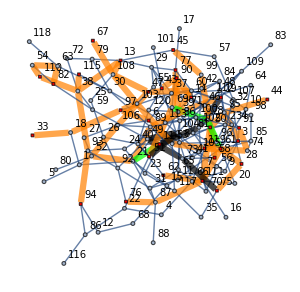
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 13947→13794

```mathematica
tree =  steinerKeyPathExchangeFixedPoint[graph100, treeMehlhorn100, terminals100];
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeMehlhorn100]

gridResultCompare[graph100,  terminals100, tree, treeMehlhorn100, edgeWeightSum[graph100, treeMehlhorn100]->edgeWeightSum[graph100, tree]]
```

```mathematica
(tree =  steinerKeyPathExchangeFixedPoint[stlibTestGraph, treeMehlhornStlibTest, stlibTestTerminals]);//AbsoluteTiming
steinerSolutionQ[tree, stlibTestTerminals]
edgeWeightSum[stlibTestGraph, tree]
edgeWeightSum[stlibTestGraph, treeMehlhornStlibTest]
```

{52.2554,Null}

True

28746

37452

```mathematica
(tree =  steinerKeyPathExchangeFixedPoint[stlibTestGraph, treeSPStlib, stlibTestTerminals]);//AbsoluteTiming
steinerSolutionQ[tree, stlibTestTerminals]
edgeWeightSum[stlibTestGraph, tree]
edgeWeightSum[stlibTestGraph, treeSPStlib]
```

{16.4211,Null}

True

28042

28895

### PEVIVE

#### Examples

```mathematica
tree =  steinerPEVIVEFixedPoint[graph15, treeKouMarkowskyBerman15, terminals15]
steinerSolutionQ[tree, terminals15]
edgeWeightSum[graph15, tree]
edgeWeightSum[graph15, treeKouMarkowskyBerman15]
```

{10<->8,8<->21,21<->2,21<->24,2<->25,1<->25,15<->24,15<->11}

True

1605

1605

{0.655423,Null}

True

13773

13947

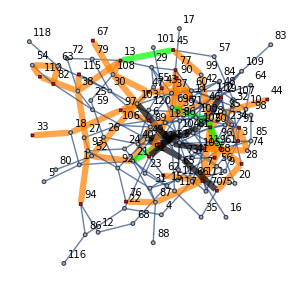
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 13947→13773

```mathematica
(tree =  steinerPEVIVEFixedPoint[graph100, treeMehlhorn100, terminals100];)//AbsoluteTiming
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeMehlhorn100]

gridResultCompare[graph100,  terminals100, tree, treeMehlhorn100,
edgeWeightSum[graph100, treeMehlhorn100]->edgeWeightSum[graph100, tree]]
```

```mathematica
(tree =  steinerPEVIVEFixedPoint[graph100, treeSP100, terminals100]);//AbsoluteTiming
steinerSolutionQ[tree, terminals100]
edgeWeightSum[graph100, tree]
edgeWeightSum[graph100, treeSP100]

gridResultCompare[graph100,  terminals100, tree, treeSP100,
edgeWeightSum[graph100, treeSP100]->edgeWeightSum[graph100, tree]]
```

{0.310518,Null}

True

13515

13515

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 13515→13515

```mathematica
(tree =  steinerPEVIVEFixedPoint[stlibTestGraph, treeMehlhornStlibTest, stlibTestTerminals]);//AbsoluteTiming
steinerSolutionQ[tree, stlibTestTerminals]
edgeWeightSum[stlibTestGraph, tree]
edgeWeightSum[stlibTestGraph, treeMehlhornStlibTest]
```

{40.2477,Null}

True

26501

37452

{3.81239,Null}

True

165

172

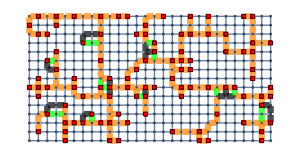
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 172→165

```mathematica
(tree = steinerPEVIVEFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid]);//AbsoluteTiming
steinerSolutionQ[tree, terminalsGrid]
edgeWeightSum[graphGrid, tree]
edgeWeightSum[graphGrid, treeMehlhornGridTest]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeMehlhornGridTest,
edgeWeightSum[graphGrid, treeMehlhornGridTest]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

### Grid graph Examples

```mathematica
tree = steinerVertexInsertionFixedPoint[graphGrid, treeSPGrid];
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeSPGrid]
```

112

112

```mathematica
tree = steinerVertexInsertionFixedPoint[graphGrid, treeMehlhornGridTest];
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeMehlhornGridTest]
```

101

101

103

105

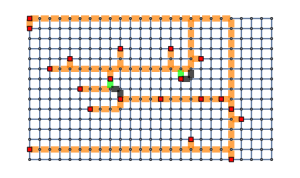
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 105→103

```mathematica
tree = steinerVertexEliminationFixedPoint[graphGrid, treeSPGrid, terminalsGrid];
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeSPGrid]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeSPGrid, edgeWeightSum[graphGrid, treeSPGrid]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

67

70

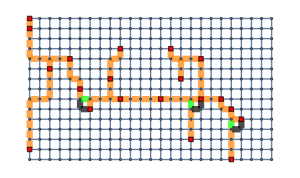
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 70→67

```mathematica
tree = steinerVertexEliminationFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid];
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeMehlhornGridTest]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeMehlhornGridTest, edgeWeightSum[graphGrid, treeMehlhornGridTest]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

True

46

47

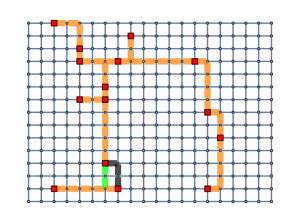
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 47→46

```mathematica
tree = steinerKeyPathExchangeFixedPoint[graphGrid, treeSPGrid, terminalsGrid];
steinerSolutionQ[tree, terminalsGrid]
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeSPGrid]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeSPGrid, edgeWeightSum[graphGrid, treeSPGrid]->edgeWeightSum[graphGrid, tree], VertexLabels->None]
```

```mathematica
gridMelhornFrames = (drawGraphSubgraphDifference[graphGrid, #⟦2⟧, #⟦1⟧, terminalsGrid, VertexLabels->None]&/@
Join[{{EdgeList@treeMehlhornGridTest, EdgeList@treeMehlhornGridTest}}, Reap[steinerKeyPathExchangeFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid], "SolutionChange"]⟦2, 1⟧]);
```

```mathematica
Export["visual/key_path_exchange_grid_mehlhorn.gif", gridMelhornFrames, "GIF" , "ControlAppearance"->None,"DisplayDurations"->1,ImageSize->700];
```

{0.323105,Null}

True

59

64

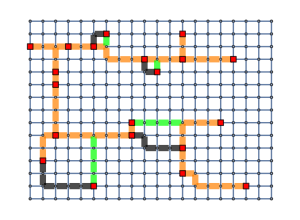
Graph | Tree | Tree weight
-Graphics- | -Graphics- | 64→59

```mathematica
(tree = steinerKeyPathExchangeFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid]);//AbsoluteTiming
steinerSolutionQ[tree, terminalsGrid]
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeMehlhornGridTest]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeMehlhornGridTest, edgeWeightSum[graphGrid, treeMehlhornGridTest]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

```mathematica
tree = steinerPEVIVEFixedPoint[graphGrid, treeSPGrid, terminalsGrid];
steinerSolutionQ[tree, terminalsGrid]
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeSPGrid]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeSPGrid, edgeWeightSum[graphGrid, treeSPGrid]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

True

47

47

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 47→47

```mathematica
tree = steinerPEVIVEFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid];
gridPEVIVEMelhornFramesReap = Append[Join[{{EdgeList@treeMehlhornGridTest, EdgeList@treeMehlhornGridTest, "START"}}, Reap[steinerPEVIVEFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid], "SolutionChange"]⟦2, 1⟧] ,{tree, tree, "END"}];

gridPEVIVEMelhornFrames = Grid[{{drawGraphSubgraphDifference[graphGrid, #⟦2⟧, #⟦1⟧, terminalsGrid, VertexLabels->None]}, {#⟦3⟧}}]&/@gridPEVIVEMelhornFramesReap;
```

```mathematica
Export["visual/presentation_mehlhorn_pevive_grid_01.gif", gridPEVIVEMelhornFrames, "GIF" , "ControlAppearance"->None,"DisplayDurations"->1,ImageSize->700];
```

```mathematica
DumpSave["dump\\presentation_mehlhorn_pevive_grid_01", gridPEVIVEMelhornFrames];
```

```mathematica
(tree = steinerPEVIVEFixedPoint[graphGrid, treeMehlhornGridTest, terminalsGrid];)//AbsoluteTiming
steinerSolutionQ[tree, terminalsGrid]
Total[edgeWeight[graphGrid, #]&/@tree]
Total[edgeWeight[graphGrid, #]&/@treeMehlhornGridTest]

gridResultCompare[graphGrid,  terminalsGrid, tree, treeMehlhornGridTest, edgeWeightSum[graphGrid, treeMehlhornGridTest]->edgeWeightSum[graphGrid, tree],
VertexLabels->None]
```

{1.54017,Null}

True

59

64

Graph | Tree | Tree weight
-Graphics- | -Graphics- | 64→59

## Computations

### Random

```mathematica
test1=testerRandom[First[runDreyfusWagner[##]]&, {{PLCHDR, PLCHDR}}, Extract[generateSteinerProblemInstanceRG[##], {{1}, {3}}]&,
Table[{10, 15, t, WeightBounds ->{1, 100000}}, {t, 3, 7, 1}], 10, False]
```

{{{{PLCHDR,PLCHDR},{10,15,3,WeightBounds→{1,100000}}},0.00629692},{{{PLCHDR,PLCHDR},{10,15,4,WeightBounds→{1,100000}}},0.0174438},{{{PLCHDR,PLCHDR},{10,15,5,WeightBounds→{1,100000}}},0.0444081},{{{PLCHDR,PLCHDR},{10,15,6,WeightBounds→{1,100000}}},0.102412},{{{PLCHDR,PLCHDR},{10,15,7,WeightBounds→{1,100000}}},0.249451}}

```mathematica
test2=testerRandom[First[runDreyfusWagner[##]]&, {{PLCHDR, PLCHDR}}, Extract[generateSteinerProblemInstanceRG[##], {{1}, {3}}]&,
Table[{100, 150, t, WeightBounds ->{1, 100000}}, {t, 3, 8, 1}], 5, False]
```

{{{{PLCHDR,PLCHDR},{100,150,3,WeightBounds→{1,100000}}},0.556973},{{{PLCHDR,PLCHDR},{100,150,4,WeightBounds→{1,100000}}},1.41357},{{{PLCHDR,PLCHDR},{100,150,5,WeightBounds→{1,100000}}},2.89826},{{{PLCHDR,PLCHDR},{100,150,6,WeightBounds→{1,100000}}},7.063},{{{PLCHDR,PLCHDR},{100,150,7,WeightBounds→{1,100000}}},15.2095},{{{PLCHDR,PLCHDR},{100,150,8,WeightBounds→{1,100000}}},33.4486}}

{{3,0.542321},{4,1.23547},{5,3.10788},{6,6.47942},{7,14.7447}}

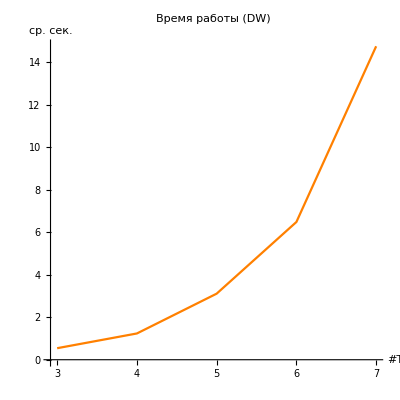

```mathematica
Transpose@{#⟦All, 1, 2, 3⟧, #⟦All, -1⟧}&@test2
ListLinePlot[%, PlotLabel-> Style["Время работы (DW)", FontSize->15, FontFamily->"Roboto Stlab"],
PlotStyle->Orange, AxesLabel->{Style["#T", FontSize->14, FontFamily->"Roboto Stlab"], Style["ср. сек.", FontSize->14, FontFamily->"Roboto Stlab"]},
AspectRatio->1]
```

```mathematica
DumpSave["dump/test_data.mx", {test1, test2}];
```

```mathematica
<<"dump/test_data.mx"
```

```mathematica
testFunctionRandom[First[runDreyfusWagner[##]]&, {PLCHDR, PLCHDR}, Extract[generateSteinerProblemInstance[##], {{1}, {3}}]&, {15, 3, BernoulliProbability->0.125}, 100, False]
```

0.0128711

```mathematica
testFunctionRandom[First[runDreyfusWagner[##]]&, {PLCHDR, PLCHDR}, Extract[generateSteinerProblemInstance[##], {{1}, {3}}]&, {100, 7, BernoulliProbability->0.1}, 1, False]
```

14.2756

```mathematica
testerRandom[First[runDreyfusWagner[##]]&, {{PLCHDR, PLCHDR}}, Extract[generateSteinerProblemInstance[##], {{1}, {3}}]&, {{15, 3, BernoulliProbability->0.125}, {50, 5, BernoulliProbability->0.08}, {100, 7, BernoulliProbability->0.05}}, 1, False]
```

{{{{PLCHDR,PLCHDR},{15,3,BernoulliProbability→0.125}},0.011905},{{{PLCHDR,PLCHDR},{50,5,BernoulliProbability→0.08}},0.760988},{{{PLCHDR,PLCHDR},{100,10,BernoulliProbability→0.05}},183.929}}

### SteinLib datasets

#### datasets

```mathematica
steinLibInstancesDList = (importSteinLibInstance[#]&/@getInstancesList["steinlib\\D"])⟦All, {1,3}⟧;
```

```mathematica
steinLibInstancesEList = (importSteinLibInstance[#]&/@getInstancesList["steinlib\\E"])⟦All, {1,3}⟧;
```

```mathematica
steinLibInstancesPUCList = (importSteinLibInstance[#]&/@getInstancesList["steinlib\\PUC"])⟦All, {1,3}⟧;
```

```mathematica
DumpSave["dump/steinlib_D.mx", {steinLibInstancesDList}];
DumpSave["dump/steinlib_E.mx", {steinLibInstancesEList}];
DumpSave["dump/steinlib_PUC.mx", {steinLibInstancesPUCList}];
```

```mathematica
<<"dump/steinlib_D.mx"
```

```mathematica
<<"dump/steinlib_E.mx"
```

```mathematica
<<"dump/steinlib_PUC.mx"
```

#### Mehlhorn

```mathematica
(steinLibInstancesDMehlhorn = tester[runMehlhorn, steinLibInstancesDList, 1, First]);//AbsoluteTiming
```

{9.35729,Null}

```mathematica
(steinLibInstancesEMehlhorn = tester[runMehlhorn, steinLibInstancesEList, 1, First]);//AbsoluteTiming
```

{23.858,Null}

```mathematica
(steinLibInstancesPUCMehlhorn = tester[runMehlhorn, steinLibInstancesPUCList, 1, First]);//AbsoluteTiming
```

{25.0065,Null}

```mathematica
DumpSave["dump/steinlib_D_Mehlhorn.mx", {steinLibInstancesDMehlhorn}];
DumpSave["dump/steinlib_E_Mehlhorn.mx", {steinLibInstancesEMehlhorn}];
DumpSave["dump/steinlib_PUC_Mehlhorn.mx", {steinLibInstancesPUCMehlhorn}];
```

```mathematica
<<"dump/steinlib_D_Mehlhorn.mx"
```

```mathematica
<<"dump/steinlib_E_Mehlhorn.mx"
```

```mathematica
<<"dump/steinlib_PUC_Mehlhorn.mx"
```

#### PEVIVE Mehlhorn

```mathematica
steinLibInstancesDMehlhornPEVIVE = tester[steinerPEVIVEFixedPoint[#1⟦1⟧, #2⟦2⟧, #1⟦2⟧]&, steinLibInstancesDMehlhorn, 1, First];
```

```mathematica
DumpSave["dump/steinlib_D_Mehlhorn_PEVIVE.mx", {steinLibInstancesDMehlhornPEVIVE}];
```

```mathematica
steinLibInstancesEMehlhornPEVIVE = tester[steinerPEVIVEFixedPoint[#1⟦1⟧, #2⟦2⟧, #1⟦2⟧]&, steinLibInstancesEMehlhorn, 1, First];
```

```mathematica
DumpSave["dump/steinlib_E_Mehlhorn_PEVIVE.mx", {steinLibInstancesEMehlhornPEVIVE}];
```

```mathematica
steinLibInstancesPUCMehlhornPEVIVE = tester[steinerPEVIVEFixedPoint[#1⟦1⟧, #2⟦2⟧, #1⟦2⟧]&, steinLibInstancesPUCMehlhorn, 1, First];
```

```mathematica
DumpSave["dump/steinlib_PUC_Mehlhorn_PEVIVE.mx", {steinLibInstancesPUCMehlhornPEVIVE}];
```

```mathematica
<<"dump/steinlib_D_Mehlhorn_PEVIVE.mx"
```

```mathematica
<<"dump/steinlib_E_Mehlhorn_PEVIVE.mx"
```

```mathematica
<<"dump/steinlib_PUC_Mehlhorn_PEVIVE.mx"
```

#### Info tables

```mathematica
steinLibInfoD = importInfoTable["steinlib\\D_info.xlsx"];
steinLibInfoE = importInfoTable["steinlib\\E_info.xlsx"];
steinLibInfoPUC = importInfoTable["steinlib\\PUC_info.xlsx"];
```

```mathematica
steinLibDVert = ToExpression/@(#["vertices"]&/@Values[steinLibInfoD]);
steinLibDEdges = ToExpression/@(#["edges"]&/@Values[steinLibInfoD]);
steinLibDTerm = ToExpression/@(#["terminals"]&/@Values[steinLibInfoD]);
steinLibDOpt = ToExpression/@(#["opt"]&/@Values[steinLibInfoD]);
```

```mathematica
steinLibEVert = ToExpression/@(#["vertices"]&/@Values[steinLibInfoE]);
steinLibEEdges = ToExpression/@(#["edges"]&/@Values[steinLibInfoE]);
steinLibETerm = ToExpression/@(#["terminals"]&/@Values[steinLibInfoE]);
steinLibEOpt = ToExpression/@(#["opt"]&/@Values[steinLibInfoE]);
```

```mathematica
steinLibPUCVert = ToExpression/@(#["vertices"]&/@Values[steinLibInfoPUC]);
steinLibPUCEdges = ToExpression/@(#["edges"]&/@Values[steinLibInfoPUC]);
steinLibPUCTerm = ToExpression/@(#["terminals"]&/@Values[steinLibInfoPUC]);
steinLibPUCOpt = ToExpression/@(#["opt"]&/@Values[steinLibInfoPUC]);
```

#### Solution info D

```mathematica
steinLibDMehlhornTime  = steinLibInstancesDMehlhorn⟦All, 2, 1⟧;
steinLibDMehlhornSolValues = edgeWeightSum@@@Transpose[{steinLibInstancesDList⟦All, 1⟧,steinLibInstancesDMehlhorn⟦All, 2, 2⟧}];
steinLibDMehlhornSolErr = N@Thread[Divide[(steinLibDMehlhornSolValues-steinLibDOpt), steinLibDOpt]];
```

```mathematica
steinLibDMehlhornTimePEVIVE  = steinLibInstancesDMehlhornPEVIVE⟦All, 2, 1⟧;
steinLibDMehlhornSolValuesPEVIVE = edgeWeightSum@@@Transpose[{steinLibInstancesDList⟦All, 1⟧,steinLibInstancesDMehlhornPEVIVE⟦All, 2, 2⟧}];
steinLibDMehlhornSolErrPEVIVE = N@Thread[Divide[(steinLibDMehlhornSolValuesPEVIVE-steinLibDOpt), steinLibDOpt]];
steinLibDMehlhornSolErrPEVIVEEnch = steinLibDMehlhornSolErr - steinLibDMehlhornSolErrPEVIVE;
```

#### Solution info E

```mathematica
steinLibEMehlhornTime  = steinLibInstancesEMehlhorn⟦All, 2, 1⟧;
steinLibEMehlhornSolValues = edgeWeightSum@@@Transpose[{steinLibInstancesEList⟦All, 1⟧,steinLibInstancesEMehlhorn⟦All, 2, 2⟧}];
steinLibEMehlhornSolErr = N@Thread[Divide[(steinLibEMehlhornSolValues-steinLibEOpt), steinLibEOpt]];
```

```mathematica
steinLibEMehlhornTimePEVIVE  = steinLibInstancesEMehlhornPEVIVE⟦All, 2, 1⟧;
steinLibEMehlhornSolValuesPEVIVE = edgeWeightSum@@@Transpose[{steinLibInstancesEList⟦All, 1⟧,steinLibInstancesEMehlhornPEVIVE⟦All, 2, 2⟧}];
steinLibEMehlhornSolErrPEVIVE = N@Thread[Divide[(steinLibEMehlhornSolValuesPEVIVE-steinLibEOpt), steinLibEOpt]];
steinLibEMehlhornSolErrPEVIVEEnch = steinLibEMehlhornSolErr - steinLibEMehlhornSolErrPEVIVE;
```

#### Solution info PUC

```mathematica
steinLibPUCMehlhornTime  = steinLibInstancesPUCMehlhorn⟦All, 2, 1⟧;
steinLibPUCMehlhornSolValues = edgeWeightSum@@@Transpose[{steinLibInstancesPUCList⟦All, 1⟧,steinLibInstancesPUCMehlhorn⟦All, 2, 2⟧}];
steinLibPUCMehlhornSolErr = N@Thread[Divide[(steinLibPUCMehlhornSolValues-steinLibPUCOpt), steinLibPUCOpt]];
```

```mathematica
steinLibPUCMehlhornTimePEVIVE  = steinLibInstancesPUCMehlhornPEVIVE⟦All, 2, 1⟧;
steinLibPUCMehlhornSolValuesPEVIVE = edgeWeightSum@@@Transpose[{steinLibInstancesPUCList⟦All, 1⟧,steinLibInstancesPUCMehlhornPEVIVE⟦All, 2, 2⟧}];
steinLibPUCMehlhornSolErrPEVIVE = N@Thread[Divide[(steinLibPUCMehlhornSolValuesPEVIVE-steinLibPUCOpt), steinLibPUCOpt]];
steinLibPUCMehlhornSolErrPEVIVEEnch = steinLibPUCMehlhornSolErr - steinLibPUCMehlhornSolErrPEVIVE;
```

#### Solution info TESTS

```mathematica
{And@@steinerSolutionQ@@@Transpose[{steinLibInstancesDMehlhorn⟦All, 2, 2⟧, steinLibInstancesDList⟦All, 2⟧}],
And@@steinerSolutionQ@@@Transpose[{steinLibInstancesEMehlhorn⟦All, 2, 2⟧, steinLibInstancesEList⟦All, 2⟧}],
And@@steinerSolutionQ@@@Transpose[{steinLibInstancesPUCMehlhorn⟦All, 2, 2⟧, steinLibInstancesPUCList⟦All, 2⟧}]}
```

{True,True,True}

```mathematica
{And@@steinerSolutionQ@@@Transpose[{steinLibInstancesDMehlhornPEVIVE⟦All, 2, 2⟧, steinLibInstancesDList⟦All, 2⟧}],
And@@steinerSolutionQ@@@Transpose[{steinLibInstancesEMehlhornPEVIVE⟦All, 2, 2⟧, steinLibInstancesEList⟦All, 2⟧}],
And@@steinerSolutionQ@@@Transpose[{steinLibInstancesPUCMehlhornPEVIVE⟦All, 2, 2⟧, steinLibInstancesPUCList⟦All, 2⟧}]
}
```

{True,True,True}

#### Result Tables

```mathematica
Grid[{{"Задача", "#Вершин", "#Ребер", "#Терминалов", "Оптимальное", "Мельхорн:", "%Ошибки ^-3", "Время (сек.)", "PEVIVE:","Доля улучшения.", "%Ошибки ^-3", "Время"}}~Join~(Transpose[{Keys@steinLibInfoD, steinLibDVert, steinLibDEdges, steinLibDTerm, steinLibDOpt, steinLibDMehlhornSolValues,PercentForm/@Round[steinLibDMehlhornSolErr, N@10^-3], Round[steinLibDMehlhornTime, N@10^-1],steinLibDMehlhornSolValuesPEVIVE,  PercentForm/@Round[steinLibDMehlhornSolErrPEVIVEEnch, N@10^-3], PercentForm/@Round[steinLibDMehlhornSolErrPEVIVE, N@10^-3], Round[steinLibDMehlhornTimePEVIVE, N@10^-1]}])~Join~{{"Среднее", "-", "-", "-", "-", "-", PercentForm@Round[Mean@steinLibDMehlhornSolErr, N@10^-3], Round[Mean@steinLibDMehlhornTime, N@10^-1], "-", PercentForm@Round[Mean@steinLibDMehlhornSolErrPEVIVEEnch, N@10^-3], PercentForm@Round[Mean@steinLibDMehlhornSolErrPEVIVE, N@10^-3], Round[Mean@steinLibDMehlhornTimePEVIVE, N@10^-1]}},
Frame->All]
```

Задача | #Вершин | #Ребер | #Терминалов | Оптимальное | Мельхорн: | %Ошибки ^-3 | Время (сек.) | PEVIVE: | Доля улучшения. | %Ошибки ^-3 | Время
d01 | 1000. | 1250. | 5. | 106. | 107 | 0.9% | 0.1 | 106 | 0.9% | 0% | 3.3
d02 | 1000. | 1250. | 10. | 220. | 237 | 7.7% | 0.1 | 229 | 3.6% | 4.1% | 7.2
d03 | 1000. | 1250. | 167. | 1565. | 1608 | 2.7% | 0.1 | 1577 | 2% | 0.8% | 21.6
d04 | 1000. | 1250. | 250. | 1935. | 1978 | 2.2% | 0.1 | 1937 | 2.1% | 0.1% | 28.3
d05 | 1000. | 1250. | 500. | 3250. | 3263 | 0.4% | 0.1 | 3256 | 0.2% | 0.2% | 27.
d06 | 1000. | 2000. | 5. | 67. | 73 | 9% | 0.1 | 71 | 3% | 6% | 4.1
d07 | 1000. | 2000. | 10. | 103. | 105 | 1.9% | 0.1 | 103 | 1.9% | 0% | 4.4
d08 | 1000. | 2000. | 167. | 1072. | 1125 | 4.9% | 0.1 | 1081 | 4.1% | 0.8% | 35.2
d09 | 1000. | 2000. | 250. | 1448. | 1513 | 4.5% | 0.2 | 1455 | 4% | 0.5% | 36.2
d10 | 1000. | 2000. | 500. | 2110. | 2133 | 1.1% | 0.2 | 2115 | 0.9% | 0.2% | 29.8
d11 | 1000. | 5000. | 5. | 29. | 31 | 6.9% | 0.2 | 30 | 3.4% | 3.4% | 4.8
d12 | 1000. | 5000. | 10. | 42. | 42 | 0% | 0.3 | 42 | 0% | 0% | 2.7
d13 | 1000. | 5000. | 167. | 500. | 524 | 4.8% | 0.4 | 509 | 3% | 1.8% | 17.1
d14 | 1000. | 5000. | 250. | 667. | 690 | 3.4% | 0.4 | 675 | 2.2% | 1.2% | 20.4
d15 | 1000. | 5000. | 500. | 1116. | 1137 | 1.9% | 0.4 | 1118 | 1.7% | 0.2% | 47.
d16 | 1000. | 25000. | 5. | 13. | 15 | 15.4% | 1.2 | 13 | 15.4% | 0% | 9.7
d17 | 1000. | 25000. | 10. | 23. | 25 | 8.7% | 1.2 | 23 | 8.7% | 0% | 11.2
d18 | 1000. | 25000. | 167. | 223. | 248 | 11.2% | 1.3 | 237 | 4.9% | 6.3% | 25.1
d19 | 1000. | 25000. | 250. | 310. | 335 | 8.1% | 1.4 | 324 | 3.5% | 4.5% | 32.2
d20 | 1000. | 25000. | 500. | 537. | 542 | 0.9% | 1.4 | 539 | 0.6% | 0.4% | 46.7
Среднее | - | - | - | - | - | 4.8% | 0.5 | - | 3.3% | 1.5% | 20.7

```mathematica
Grid[{{"Задача", "#Вершин", "#Ребер", "#Терминалов", "Оптимальное", "Мельхорн:", "%Ошибки ^-3", "Время (сек.)", "PEVIVE:","Доля улучшения.", "%Ошибки ^-3", "Время"}}~Join~(Transpose[{Keys@steinLibInfoE, steinLibEVert, steinLibEEdges, steinLibETerm, steinLibEOpt, steinLibEMehlhornSolValues,PercentForm/@Round[steinLibEMehlhornSolErr, N@10^-3], Round[steinLibEMehlhornTime, N@10^-1],steinLibEMehlhornSolValuesPEVIVE,  PercentForm/@Round[steinLibEMehlhornSolErrPEVIVEEnch, N@10^-3], PercentForm/@Round[steinLibEMehlhornSolErrPEVIVE, N@10^-3], Round[steinLibEMehlhornTimePEVIVE, N@10^-1]}])~Join~{{"Среднее", "-", "-", "-", "-", "-",PercentForm@Round[Mean@steinLibEMehlhornSolErr, N@10^-3], Round[Mean@steinLibEMehlhornTime, N@10^-1], "-", PercentForm@Round[Mean@steinLibEMehlhornSolErrPEVIVEEnch, N@10^-3], PercentForm@Round[Mean@steinLibEMehlhornSolErrPEVIVE, N@10^-3], Round[Mean@steinLibEMehlhornTimePEVIVE, N@10^-1]}},
Frame->All]
```

Задача | #Вершин | #Ребер | #Терминалов | Оптимальное | Мельхорн: | %Ошибки ^-3 | Время (сек.) | PEVIVE: | Доля улучшения. | %Ошибки ^-3 | Время
e01 | 2500. | 3125. | 5. | 111. | 125 | 12.6% | 0.2 | 111 | 12.6% | 0% | 14.3
e02 | 2500. | 3125. | 10. | 214. | 255 | 19.2% | 0.2 | 231 | 11.2% | 7.9% | 16.7
e03 | 2500. | 3125. | 417. | 4013. | 4171 | 3.9% | 0.3 | 4041 | 3.2% | 0.7% | 172.6
e04 | 2500. | 3125. | 625. | 5101. | 5204 | 2% | 0.3 | 5121 | 1.6% | 0.4% | 259.9
e05 | 2500. | 3125. | 1250. | 8128. | 8174 | 0.6% | 0.4 | 8135 | 0.5% | 0.1% | 267.3
e06 | 2500. | 5000. | 5. | 73. | 84 | 15.1% | 0.3 | 73 | 15.1% | 0% | 14.3
e07 | 2500. | 5000. | 10. | 145. | 165 | 13.8% | 0.3 | 152 | 9% | 4.8% | 15.9
e08 | 2500. | 5000. | 417. | 2640. | 2742 | 3.9% | 0.4 | 2660 | 3.1% | 0.8% | 202.4
e09 | 2500. | 5000. | 625. | 3604. | 3719 | 3.2% | 0.4 | 3626 | 2.6% | 0.6% | 179.7
e10 | 2500. | 5000. | 1250. | 5600. | 5647 | 0.8% | 0.5 | 5609 | 0.7% | 0.2% | 397.2
e11 | 2500. | 12500. | 5. | 34. | 39 | 14.7% | 0.6 | 37 | 5.9% | 8.8% | 11.9
e12 | 2500. | 12500. | 10. | 67. | 70 | 4.5% | 0.6 | 68 | 3% | 1.5% | 20.2
e13 | 2500. | 12500. | 417. | 1280. | 1351 | 5.5% | 0.8 | 1313 | 3% | 2.6% | 129.5
e14 | 2500. | 12500. | 625. | 1732. | 1796 | 3.7% | 0.8 | 1742 | 3.1% | 0.6% | 275.6
e15 | 2500. | 12500. | 1250. | 2784. | 2817 | 1.2% | 0.9 | 2791 | 0.9% | 0.3% | 259.1
e16 | 2500. | 62500. | 5. | 15. | 18 | 20% | 3.5 | 15 | 20% | 0% | 38.2
e17 | 2500. | 62500. | 10. | 25. | 27 | 8% | 3. | 25 | 8% | 0% | 27.1
e18 | 2500. | 62500. | 417. | 564. | 628 | 11.3% | 3.3 | 597 | 5.5% | 5.9% | 136.1
e19 | 2500. | 62500. | 625. | 758. | 800 | 5.5% | 3.4 | 769 | 4.1% | 1.5% | 166.7
e20 | 2500. | 62500. | 1250. | 1342. | 1355 | 1% | 3.6 | 1349 | 0.4% | 0.5% | 285.
Среднее | - | - | - | - | - | 7.5% | 1.2 | - | 5.7% | 1.9% | 144.5

```mathematica
Grid[{{"Задача", "#Вершин", "#Ребер", "#Терминалов", "Оптимальное", "Мельхорн:", "%Ошибки ^-3", "Время (сек.)", "PEVIVE:","Доля улучшения.", "%Ошибки ^-3", "Время"}}~Join~(Transpose[{Keys@steinLibInfoPUC, steinLibPUCVert, steinLibPUCEdges, steinLibPUCTerm, steinLibPUCOpt, steinLibPUCMehlhornSolValues,PercentForm/@Round[steinLibPUCMehlhornSolErr, N@10^-3], Round[steinLibPUCMehlhornTime, N@10^-1],steinLibPUCMehlhornSolValuesPEVIVE,  PercentForm/@Round[steinLibPUCMehlhornSolErrPEVIVEEnch, N@10^-3], PercentForm/@Round[steinLibPUCMehlhornSolErrPEVIVE, N@10^-3], Round[steinLibPUCMehlhornTimePEVIVE, N@10^-1]}])~Join~{{"Среднее", "-", "-", "-", "-", "-", PercentForm@Round[Mean@steinLibPUCMehlhornSolErr, N@10^-3], Round[Mean@steinLibPUCMehlhornTime, N@10^-1], "-", PercentForm@Round[Mean@steinLibPUCMehlhornSolErrPEVIVEEnch, N@10^-3], PercentForm@Round[Mean@steinLibPUCMehlhornSolErrPEVIVE, N@10^-3], Round[Mean@steinLibPUCMehlhornTimePEVIVE, N@10^-1]}},
Frame->All]
```

Задача | #Вершин | #Ребер | #Терминалов | Оптимальное | Мельхорн: | %Ошибки ^-3 | Время (сек.) | PEVIVE: | Доля улучшения. | %Ошибки ^-3 | Время
bip42p | 1200. | 3982. | 200. | 24657. | 34622 | 40.4% | 0.3 | 26745 | 31.9% | 8.5% | 18.1
bip42u | 1200. | 3982. | 200. | 236. | 304 | 28.8% | 0.3 | 271 | 14% | 14.8% | 13.8
bip52p | 2200. | 7997. | 200. | 24526. | 37452 | 52.7% | 0.5 | 26501 | 44.7% | 8.1% | 33.9
bip52u | 2200. | 7997. | 200. | 234. | 296 | 26.5% | 0.5 | 268 | 12% | 14.5% | 24.9
bip62p | 1200. | 10002. | 200. | 22843. | 35356 | 54.8% | 0.7 | 24273 | 48.5% | 6.3% | 21.1
bip62u | 1200. | 10002. | 200. | 219. | 250 | 14.2% | 0.6 | 238 | 5.5% | 8.7% | 14.6
bipa2p | 3300. | 18073. | 300. | 35326. | 54871 | 55.3% | 1.1 | 37930 | 48% | 7.4% | 84.6
bipa2u | 3300. | 18073. | 300. | 338. | 407 | 20.4% | 1. | 379 | 8.3% | 12.1% | 62.4
bipe2p | 550. | 5013. | 50. | 5616. | 9090 | 61.9% | 0.3 | 6064 | 53.9% | 8% | 3.6
bipe2u | 550. | 5013. | 50. | 54. | 59 | 9.3% | 0.3 | 58 | 1.9% | 7.4% | 3.1
cc10-2p | 1024. | 5120. | 135. | 35297. | 43074 | 22% | 0.3 | 37383 | 16.1% | 5.9% | 27.4
cc10-2u | 1024. | 5120. | 135. | 342. | 430 | 25.7% | 0.3 | 374 | 16.4% | 9.4% | 19.3
cc11-2p | 2048. | 11263. | 244. | 63491. | 78494 | 23.6% | 0.6 | 67241 | 17.7% | 5.9% | 109.
cc11-2u | 2048. | 11263. | 244. | 612. | 789 | 28.9% | 0.6 | 672 | 19.1% | 9.8% | 66.8
cc12-2p | 4096. | 24574. | 473. | 121106. | 152916 | 26.3% | 1.4 | 128726 | 20% | 6.3% | 547.5
cc12-2u | 4096. | 24574. | 473. | 1172. | 1464 | 24.9% | 1.4 | 1289 | 14.9% | 10% | 237.4
cc3-10p | 1000. | 13500. | 50. | 12772. | 15798 | 23.7% | 0.7 | 13553 | 17.6% | 6.1% | 17.
cc3-10u | 1000. | 13500. | 50. | 125. | 145 | 16% | 0.7 | 138 | 5.6% | 10.4% | 11.6
cc3-11p | 1331. | 19965. | 61. | 15582. | 18632 | 19.6% | 0.9 | 16213 | 15.5% | 4% | 23.4
cc3-11u | 1331. | 19965. | 61. | 153. | 184 | 20.3% | 0.9 | 166 | 11.8% | 8.5% | 18.3
cc3-12p | 1728. | 28512. | 74. | 18826. | 22390 | 18.9% | 1.3 | 19617 | 14.7% | 4.2% | 33.6
cc3-12u | 1728. | 28512. | 74. | 185. | 214 | 15.7% | 1.1 | 197 | 9.2% | 6.5% | 16.6
cc3-4p | 64. | 288. | 8. | 2338. | 2439 | 4.3% | 0. | 2343 | 4.1% | 0.2% | 0.2
cc3-4u | 64. | 288. | 8. | 23. | 24 | 4.3% | 0. | 23 | 4.3% | 0% | 0.2
cc3-5p | 125. | 750. | 13. | 3661. | 4371 | 19.4% | 0. | 3675 | 19% | 0.4% | 0.8
cc3-5u | 125. | 750. | 13. | 36. | 38 | 5.6% | 0. | 36 | 5.6% | 0% | 0.5
cc5-3p | 243. | 1215. | 27. | 7299. | 8910 | 22.1% | 0.1 | 7973 | 12.8% | 9.2% | 2.5
cc5-3u | 243. | 1215. | 27. | 71. | 88 | 23.9% | 0.1 | 80 | 11.3% | 12.7% | 1.2
cc6-2p | 64. | 192. | 12. | 3271. | 4001 | 22.3% | 0. | 3374 | 19.2% | 3.1% | 0.4
cc6-2u | 64. | 192. | 12. | 32. | 36 | 12.5% | 0. | 35 | 3.1% | 9.4% | 0.3
cc6-3p | 729. | 4368. | 76. | 20270. | 25264 | 24.6% | 0.3 | 21456 | 18.8% | 5.9% | 11.2
cc6-3u | 729. | 4368. | 76. | 197. | 246 | 24.9% | 0.2 | 217 | 14.7% | 10.2% | 8.2
cc7-3p | 2187. | 15308. | 222. | 56799. | 71249 | 25.4% | 0.8 | 59970 | 19.9% | 5.6% | 96.8
cc7-3u | 2187. | 15308. | 222. | 549. | 702 | 27.9% | 0.8 | 611 | 16.6% | 11.3% | 79.3
cc9-2p | 512. | 2304. | 64. | 17199. | 22357 | 30% | 0.1 | 18577 | 22% | 8% | 10.2
cc9-2u | 512. | 2304. | 64. | 167. | 225 | 34.7% | 0.1 | 185 | 24% | 10.8% | 8.8
hc10p | 1024. | 5120. | 512. | 59797. | 81171 | 35.7% | 0.4 | 62548 | 31.1% | 4.6% | 74.5
hc10u | 1024. | 5120. | 512. | 575. | 751 | 30.6% | 0.4 | 634 | 20.3% | 10.3% | 39.8
hc11p | 2048. | 11264. | 1024. | 119492. | 160843 | 34.6% | 0.9 | 122974 | 31.7% | 2.9% | 456.5
hc11u | 2048. | 11264. | 1024. | 1145. | 1514 | 32.2% | 0.8 | 1276 | 20.8% | 11.4% | 200.3
hc12p | 4096. | 24576. | 2048. | 236949. | 321168 | 35.5% | 1.8 | 244411 | 32.4% | 3.1% | 4047.7
hc12u | 4096. | 24576. | 2048. | 2262. | 3034 | 34.1% | 1.8 | 2548 | 21.5% | 12.6% | 1145.4
hc6p | 64. | 192. | 32. | 4003. | 4973 | 24.2% | 0. | 4128 | 21.1% | 3.1% | 0.4
hc6u | 64. | 192. | 32. | 39. | 45 | 15.4% | 0. | 39 | 15.4% | 0% | 0.3
hc7p | 128. | 448. | 64. | 7905. | 9912 | 25.4% | 0. | 7953 | 24.8% | 0.6% | 1.
hc7u | 128. | 448. | 64. | 77. | 94 | 22.1% | 0. | 81 | 16.9% | 5.2% | 1.
hc8p | 256. | 1024. | 128. | 15322. | 20201 | 31.8% | 0.1 | 15956 | 27.7% | 4.1% | 3.2
hc8u | 256. | 1024. | 128. | 148. | 184 | 24.3% | 0.1 | 160 | 16.2% | 8.1% | 2.7
hc9p | 512. | 2304. | 256. | 30242. | 40257 | 33.1% | 0.2 | 31686 | 28.3% | 4.8% | 13.9
hc9u | 512. | 2304. | 256. | 292. | 371 | 27.1% | 0.2 | 317 | 18.5% | 8.6% | 9.8
Среднее | - | - | - | - | - | 26.4% | 0.5 | - | 19.4% | 7% | 152.5

```mathematica
Grid[
{
{SpanFromLeft,  "Средняя ошибка",SpanFromLeft},
{"Dataset", "D", "E", "PUC"},
{"Мельхорн"}~Join~{
PercentForm@Round[Mean@steinLibDMehlhornSolErr, N@10^-3],
PercentForm@Round[Mean@steinLibEMehlhornSolErr, N@10^-3],
PercentForm@Round[Mean@steinLibPUCMehlhornSolErr, N@10^-3]},
{"PEVIVE"}~Join~{
PercentForm@Round[Mean@steinLibDMehlhornSolErrPEVIVE, N@10^-3],
PercentForm@Round[Mean@steinLibEMehlhornSolErrPEVIVE, N@10^-3],
PercentForm@Round[Mean@steinLibPUCMehlhornSolErrPEVIVE, N@10^-3]}
},
Frame->All]
```

| Средняя ошибка |  | 
Dataset | D | E | PUC
Мельхорн | 4.8% | 7.5% | 26.4%
PEVIVE | 1.5% | 1.9% | 7%

```mathematica
Grid[
{
{SpanFromLeft,  Style["Состав данных", FontSize->10, FontFamily->"Roboto Slab"],SpanFromLeft},
Style[#, FontSize->10, FontFamily->"Roboto Slab"]&/@{"Dataset", "D", "E", "PUC"},
Style[#, FontSize->10, FontFamily->"Roboto Slab"]&/@{"Вершины", "1000", "2500", "≤4096"},
Style[#, FontSize->10, FontFamily->"Roboto Slab"]&/@{"Ребра", "≤25000", "≤64000", "≤28512"},
Style[#, FontSize->10, FontFamily->"Roboto Slab"]&/@{"Терминалы", "≤500", "≤1250", "≤2048"}
},
Frame->All]
```

| Состав данных |  | 
Dataset | D | E | PUC
Вершины | 1000 | 2500 | ≤4096
Ребра | ≤25000 | ≤64000 | ≤28512
Терминалы | ≤500 | ≤1250 | ≤2048

## Charts

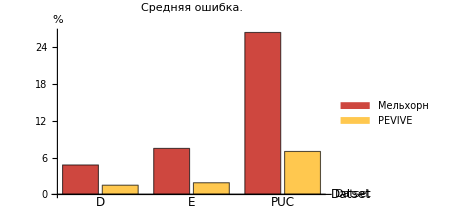

```mathematica
errChart = BarChart[100*Transpose@{{
Round[Mean@steinLibDMehlhornSolErr, N@10^-3],
Round[Mean@steinLibEMehlhornSolErr, N@10^-3],
Round[Mean@steinLibPUCMehlhornSolErr, N@10^-3]},
{Round[Mean@steinLibDMehlhornSolErrPEVIVE, N@10^-3],
Round[Mean@steinLibEMehlhornSolErrPEVIVE, N@10^-3],
Round[Mean@steinLibPUCMehlhornSolErrPEVIVE, N@10^-3]}
},
ChartStyle->Table[ColorData["SunsetColors"][k], {k, 0.35, 0.8, 0.4}],
ChartLegends->Placed[(Style[#, FontSize->12, FontFamily->"Roboto Slab"]&/@{"Мельхорн", "PEVIVE"}), Below],
PlotLabel->Style["Средняя ошибка.", FontSize->14, FontFamily->"Roboto Slab"],
ChartLabels->{Style[#, FontSize->12, FontFamily->"Roboto Slab"]&/@{"D","E","PUC"}, None},
AxesLabel->(Style[#, FontSize->12, FontFamily->"Roboto Slab"]&/@{"Datset", "%"}),
ImageSize->350
]
```

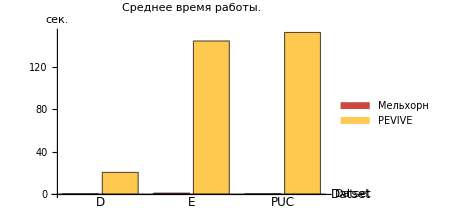

```mathematica
timeChart = BarChart[Transpose@{{
Round[Mean@steinLibDMehlhornTime, N@10^-1],
Round[Mean@steinLibEMehlhornTime, N@10^-1],
Round[Mean@steinLibPUCMehlhornTime, N@10^-1]},
{Round[Mean@steinLibDMehlhornTimePEVIVE, N@10^-1],
Round[Mean@steinLibEMehlhornTimePEVIVE, N@10^-1],
Round[Mean@steinLibPUCMehlhornTimePEVIVE, N@10^-1]}
},
ChartStyle->Table[ColorData["SunsetColors"][k], {k, 0.35, 0.8, 0.4}],
ChartLegends->Placed[(Style[#, FontSize->12, FontFamily->"Roboto Slab"]&/@{"Мельхорн", "PEVIVE"}), Below],
PlotLabel->Style["Среднее время работы.", FontSize->14, FontFamily->"Roboto Slab"],
ChartLabels->{Style[#, FontSize->12, FontFamily->"Roboto Slab"]&/@{"D","E","PUC"}, None},
AxesLabel->(Style[#, FontSize->12, FontFamily->"Roboto Slab"]&/@{"Datset", "сек."}),
ImageSize->350
]
```

```mathematica
compCharts = Grid[{{errChart, timeChart}}]
```

-Graphics- | -Graphics-

```mathematica
DumpSave["dump\\compCharts", compCharts];
```

## References

[1] * Корте Б. Комбинаторная оптимизация. Теория и Алгоритмы / Бернард Корте, Йенс Фиген ; перевод с англ. М.А. Бабенко ; - М. : МЦНМО ; 2015 - 720 с.
[2] Markowski G. A fast algorithm for steiner trees / G. Markowski, L. Kou, L. Berman ; 1981.
[3] ^Fuchs B. Speeding up the Dreyfus-Wagner Algorithmfor minimum Steiner trees / B. Fuchs, W. Kern, X. Wang ; 2007
[4] *^ Fomin F.  Computing Optimal Steiner Trees in Polynomial Space / F. Fomin, F. Grandoni, D. Kratsch, D. Lokshtanov, S.Saurabh ; 2012
[5] Dreyfus S.  The Steiner Problem in Graphs / S. Dreyfus, R. Wagner ; 1971
[6] Plesnik J. Heuristics for the Steiner problem in graphs / J. Plesnik ; 1989
[7] *$ Uchoa E. Fast Local Search for Steiner Trees in Graphs / E. Uchoa, R. Werneck  ; 2010
[8] Mehlhorn K. A Faster Approximation Algorithm for the Steiner Tree Problem in Graphs / K. Mehlhorn ; 1988

^ - more theoretical
$ - more practical
* - nice paper